LAST EDITED:

```mathematica
Now
```

Wed 19 Apr 2023 06:37:31GMT-6

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
color={Orange,Blue,Red,Gray,Black,Magenta,Brown,Purple,Darker[Yellow]};
```

#### parametro de impacto

```mathematica
bdat=Import["b.csv"];
bdat[[1]]
```

{b,DLE,DLE error,DLH,DLH error,DL,Dl error}

```mathematica
bdat[[1]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,f}
```

{b,DL}

```mathematica
nn=4;
b=bdat[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,Abs[f]*10^15*10^nn};
berror=bdat[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,Abs[g]*10^15*10^nn};
DL=Table[{i,10^-4*10^nn},{i,1.4,10.5}];
```

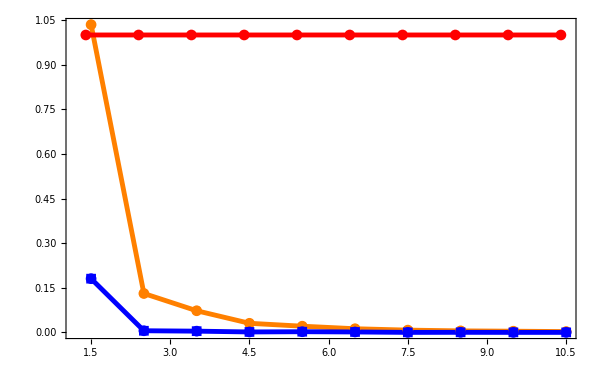

```mathematica
DL=Table[{i,10^-4*10^nn},{i,1.4,10.5}];
ListPlot[{b,berror, DL}, PlotRange->All,
(*Epilog->{Red,Thick,  Line[{{0,10^-4*10^nn},{11,10^-4*10^nn}}]},*)
Joined->True,
Mesh->All,
PlotMarkers->{Automatic,10},
Frame->True,
FrameLabel->{MaTeX["b\\text{ [nm]}",FontSize->25],MaTeX["\\Delta L \\times 10^{-4}\\,\\hbar",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}}(*,
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{without size correction}","\\text{with size correction}"},FontSize->20],
LegendLabel->MaTeX["\\text{Dielectric function}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.77,0.82}]*),
ImageSize->600,
PlotLegends->Placed[LineLegend[MaTeX[{"\\Delta L_{\\rm ext} (\\times 10^{15})","\\text{error } \\Delta L_{\\rm ext} (\\times 10^{15})", "\\text{mín. } \\Delta L"},FontSize->20],
LegendLabel->Column@MaTeX[{"v=0.5\\,c"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.81,0.50}]]
```

#### velocidad

```mathematica
vdat=Import["v.csv"];
```

```mathematica
vdat[[1]]
```

{v,DLE,DLE error,DLH,DLH error,DL,DL error,}

```mathematica
vdat[[1]]/.{a_,b_,c_,d_,e_,f_,g_,h_}->{a,f}
```

{v,DL}

```mathematica
nn=4;
mm=16;
v=vdat[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_}->{a,Abs[f]*10^mm*10^nn};
verror=vdat[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_}->{a,Abs[g]*10^mm*10^nn};
DL=Table[{i,10^-4*10^nn},{i,0.09,0.9,0.1}];
```

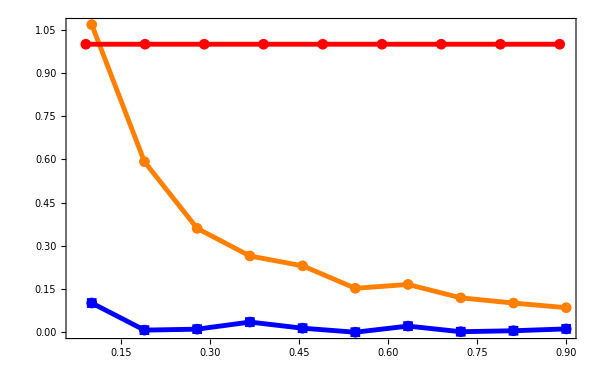

```mathematica
DL=Table[{i,10^-4*10^nn},{i,0.09,0.9,0.1}];
ListPlot[{v,verror, DL}, PlotRange->All,
(*Epilog->{Red,Thick,  Line[{{0,10^-4*10^nn},{11,10^-4*10^nn}}]},*)
Joined->True,
Mesh->All,
PlotMarkers->{Automatic,10},
Frame->True,
FrameLabel->{MaTeX["v/c",FontSize->25],MaTeX["\\Delta L \\times 10^{-4}\\,\\hbar",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}}(*,
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{without size correction}","\\text{with size correction}"},FontSize->20],
LegendLabel->MaTeX["\\text{Dielectric function}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.77,0.82}]*),
ImageSize->600,
PlotLegends->Placed[LineLegend[MaTeX[{"\\Delta L_{\\rm ext} (\\times 10^{16})","\\text{error } \\Delta L_{\\rm ext} (\\times 10^{16})", "\\text{mín. } \\Delta L"},FontSize->20],
LegendLabel->Column@MaTeX[{"b=5.5 \\,\\text{nm}"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.81,0.51}]]
```

#### integration surface

```mathematica
rdat=Import["r.csv"];
```

```mathematica
rdat[[1]]
```

{r,DLE,DLE error,DLH,DLHerror,DL,Dlerror}

```mathematica
rdat[[1]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,f}
```

{r,DL}

```mathematica
nn=4;
mm=14;
r=rdat[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,Abs[f]*10^mm*10^nn};
rerror=rdat[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,Abs[g]*10^(mm+1)*10^nn};
DL=Table[{i,10^-4*10^nn},{i,0,50}];
```

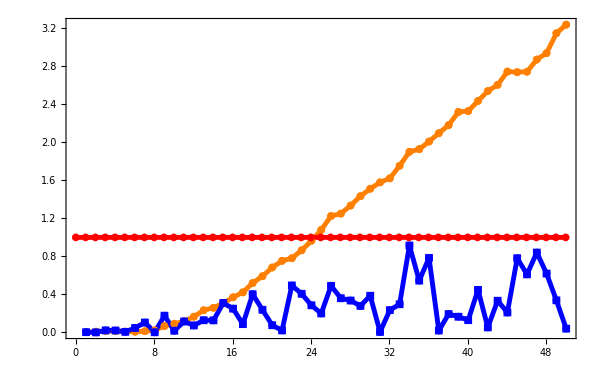

```mathematica
ListPlot[{r,rerror, DL}, PlotRange->All,
Joined->True,
Mesh->All,
PlotMarkers->{Automatic,8},
Frame->True,
FrameLabel->{MaTeX["R\\text{ [nm]}",FontSize->25],MaTeX["\\Delta L \\times 10^{-4}\\,\\hbar",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}}(*,
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{without size correction}","\\text{with size correction}"},FontSize->20],
LegendLabel->MaTeX["\\text{Dielectric function}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.77,0.82}]*),
ImageSize->600,
PlotLegends->Placed[LineLegend[MaTeX[{"\\Delta L_{\\rm ext} (\\times 10^{14})","\\text{error } \\Delta L_{\\rm ext} (\\times 10^{15})", "\\text{mín. } \\Delta L"},FontSize->20],
LegendLabel->Column@MaTeX[{"b=R + 0.45 \\,\\text{nm}"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.23,0.69}]]
```

#### multipoles

```mathematica
ldat=Import["l.csv"];
```

```mathematica
ldat[[1]]
```

{l,DLE,DLEerror,DLH,DLHerror,DL,Dlerror}

```mathematica
ldat[[1]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,f}
```

{l,DL}

```mathematica
nn=4;
mm=16;
l=ldat[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,Abs[f]*10^mm*10^nn};
lerror=ldat[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_}->{a,Abs[g]*10^(mm+1)*10^nn};
DL=Table[{i,10^-4*10^nn},{i,1,10}];
```

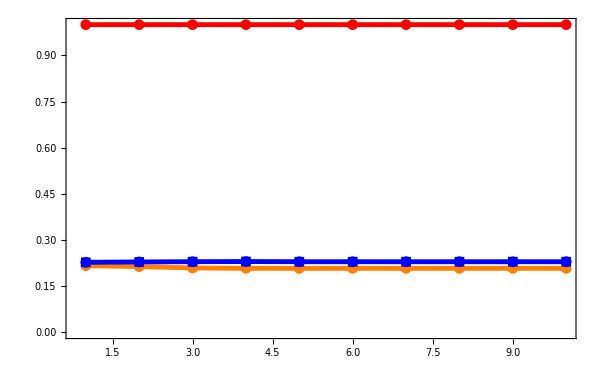

```mathematica
ListPlot[{l,lerror, DL}, PlotRange->All,
Joined->True,
Mesh->All,
PlotMarkers->{Automatic,10},
Frame->True,
FrameLabel->{MaTeX["\\ell",FontSize->25],MaTeX["\\Delta L \\times 10^{-4}\\,\\hbar",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}}(*,
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{without size correction}","\\text{with size correction}"},FontSize->20],
LegendLabel->MaTeX["\\text{Dielectric function}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.77,0.82}]*),
ImageSize->600,
PlotLegends->Placed[LineLegend[MaTeX[{"\\Delta L_{\\rm ext} (\\times 10^{16})","\\text{error } \\Delta L_{\\rm ext} (\\times 10^{17})", "\\text{mín. } \\Delta L"},FontSize->20],
LegendLabel->Column@MaTeX[{"b=5.5 \\,\\text{nm}, \\, v = 0.5 \\, c"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.77,0.59}]]
```